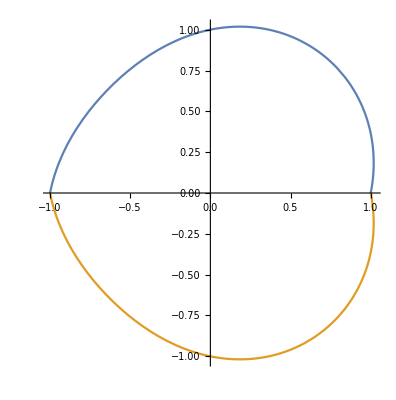

```mathematica
d=.1;
ParametricPlot[{{(1+d*Sin[t])Cos[t/2],(1+d*Sin[t])Sin[t/2]},{(1-d*Sin[t])Cos[t/2+Pi],(1-d*Sin[t])Sin[t/2+Pi]}},{t,0,2Pi}]
```

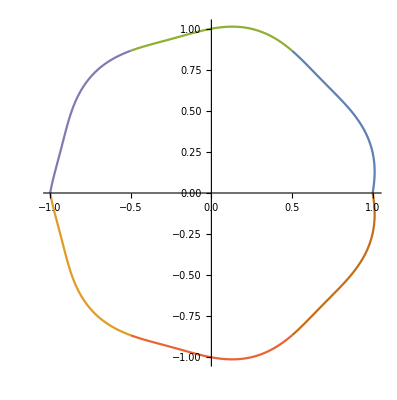

```mathematica
d=.03;
ParametricPlot[{
{(1+d*Sin[t])Cos[t/6],(1+d*Sin[t])Sin[t/6]},
{(1-d*Sin[t])Cos[t/6+Pi],(1-d*Sin[t])Sin[t/6+Pi]},

{(1+d*Sin[t])Cos[t/6+Pi/3],(1+d*Sin[t])Sin[t/6+Pi/3]},
{(1-d*Sin[t])Cos[t/6+Pi/3+Pi],(1-d*Sin[t])Sin[t/6+Pi/3+Pi]},

{(1+d*Sin[t])Cos[t/6+2Pi/3],(1+d*Sin[t])Sin[t/6+2Pi/3]},
{(1-d*Sin[t])Cos[t/6+2Pi/3+Pi],(1-d*Sin[t])Sin[t/6+2Pi/3+Pi]},
},{t,0,2Pi}]
```